```mathematica
L1 = {116.60, 116.50, 116.50};
L2 = {7.40, 7.45, 7.45};
Ug = {0.003,0.023,0.041,0.057,0.092,0.107, 0.120} ;
l1 = Mean[L1];
l2 = Mean[L2];
L = l1 - l2
mass = {0, 100, 200, 300, 400, 500, 600};
lo= 12.601;
l = {12.601, 12.780, 12.980, 13.192, 13.396, 13.575, 13.800};
deltaL =(l - lo) ;
actualDeltaL = deltaL* (L/l1)
```

109.1

{0.,0.167582,0.354825,0.553302,0.744289,0.911871,1.12252}

```mathematica
fitDataA = Transpose[{mass, actualDeltaL}];
fitA = LinearModelFit[fitDataA, x, x]
%["ParameterTable"]
line = Fit[fitDataA, {1, x}, x]
Show[ListPlot[fitDataA, PlotStyle->Black, PlotMarkers->{Style["X",10]}],
Plot[line, {x, 0, 650}, PlotStyle->Gray],
AxesLabel->{Style["质量(g)",15,Bold], Style["ΔL(mm)", 15, Bold]},
PlotLabel->Style["砝码质量与金属丝伸长量关系的拟合曲线",18,FontFamily->"Hack Nerd Font", Bold],
AxesStyle->Directive[Arrowheads[0.05],13],
ImageSize->Large]
```

FittedModel[-0.0114017+0.00187343 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | -0.0114017 | 0.00744231 | -1.53202 | 0.186087
x | 0.00187343 | 0.0000206413 | 90.7614 | 3.07775×10^-9

-0.0114017+0.00187343 x

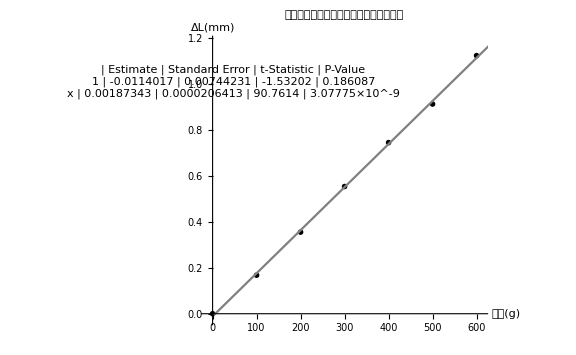

```mathematica
fitDataB = Transpose[{actualDeltaL, Ug}];
fitB = LinearModelFit[fitDataB,x,x]
%["ParameterTable"]
lineB = Fit[fitDataB, {1,x},x]
Show[ListPlot[fitDataB,PlotStyle->Black,PlotMarkers->{Style["X",10]}],
Plot[lineB, {x,0,1.2},PlotStyle->Gray],
AxesLabel->{Style["金属丝实际伸长长度(mm)",15,Bold],Style["Ug(mV)",15,Bold]},
PlotLabel->Style["Ug与金属丝实际伸长长度拟合曲线",18,FontFamily->"Hack Nerd Font",Bold],
ImageSize->Large]
```

FittedModel[0.00350386+0.108571 x]

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.00350386 | 0.00373336 | 0.938529 | 0.391061
x | 0.108571 | 0.00560496 | 19.3704 | 6.76524×10^-6

0.00350386+0.108571 x

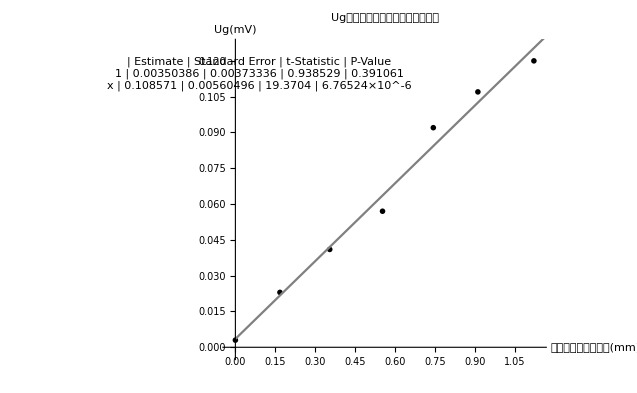

```mathematica
9.975*1.091/(Pi*0.0019)
```

1823.2

```mathematica
1823.1994505892071
10.08*4*51*1.091/(34.73*0.402)
```

1823.2

160.688

```mathematica
51-19.73
```

31.27